# Mathematica notebook: numerical calculation of linearized NLS spectrum.

The code below defined the rational function  such that  for  a solution to the NLS standing wave equation. By Galilean invariance the traveling waves can be mapped to standing waves with no change in stability.

```mathematica
Clear[l];Clear[m];Clear[Period]
l = .75;m=-.25;
κ=Sqrt[-l m (1+l+m)];
En = -1/2 (1+l)(1+m)(l+m);
ω=-(1+l+l^2+m+l m+m^2);c=0;ζ=3; f[x_] := x^2; F[x_] := x^3/3;fp[x_] := 2x;NModes = 20;
(* There are 2 NModes+1 Fourier modes, from k= -NModes to k=NModes *)
(* Begin by numerically solving traveling wave ODE *)
Poly[x_,En_,ω_,κ_,c_,ζ_] := 2 En - (ω+ c^2/4)  x^2 - κ^2 /x^2 - ζ F[x^2]
```

```mathematica
rts[En_,ω_,κ_,c_,ζ_]:=Sort[DeleteDuplicates[Abs[x /. NSolve[Poly[x,En,ω,κ,c,ζ]==0,x , Reals,WorkingPrecision->15]]]]
```

```mathematica
tplist=rts[En,ω,κ,c,ζ]
Period[En_,ω_,κ_,c_,ζ_]:= NIntegrate[2/Sqrt[Poly[x,En,ω,κ,c,ζ]],{x,tplist[[1]],tplist[[2]]},WorkingPrecision->15]
```

{0.866025403784439,1.}

```mathematica
Mass[En_,ω_,κ_,c_,ζ_]:= NIntegrate[2x^2/Sqrt[Poly[x,En,ω,κ,c,ζ]],{x,tplist[[1]],tplist[[2]]},WorkingPrecision->15]
FExp[En_,ω_,κ_,c_,ζ_]:= NIntegrate[2κ x^-2/Sqrt[Poly[x,En,ω,κ,c,ζ]],{x,tplist[[1]],tplist[[2]]},WorkingPrecision->15]
```

```mathematica
M = Mass[En,ω,κ,c,ζ]
T=Period[En,ω,κ,c,ζ]
η = FExp[En,ω,κ,c,ζ]- c T/2
```

1.67784647909938

1.92884614183376

1.1881540796616

```mathematica
Sol =NDSolve[{A''[x] - κ^2/(A[x])^3 + (ω+c^2/4) A[x] + ζ f[A[x]^2] A[x]==0,S'[x]-κ/(A[x])^2 ==0,A[0]== tplist[[1]],A'[0]==0,S[0]==0},{A,S},{x,0,T},WorkingPrecision->15]
```

NDSolve::precw: The precision of the differential equation ({{-0.28125/A[x]^3-1.9375 A[x]+3 A[x]^5+A''[x]==0,-0.53033/A[x]^2+S'[x]==0,A[0]==«44»,A'[0]==0,S[0]==0},{},{},{},{}}) is less than WorkingPrecision (15.).

{{A→InterpolatingFunction[…],S→InterpolatingFunction[…]}}

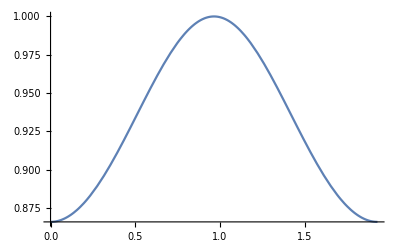

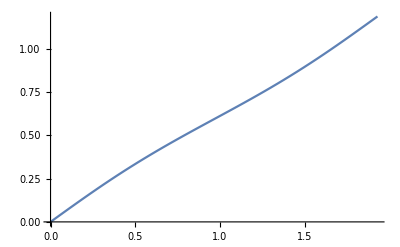

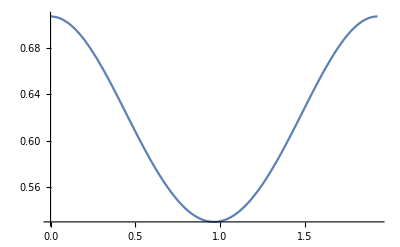

```mathematica
Plot[Evaluate[A[x]/.Sol],{x,0,T}]
Plot[Evaluate[S[x]/.Sol],{x,0,T}]
Plot[κ/(A[x])^2/. Sol,{x,0,T}]
```

```mathematica
NIntegrate[A[x]^2 /. Sol,{x,0,T}]
```

{1.67785}

Compute the Fourier series coefficients of the standing wave solutions (amplitude and phase) by numerical quadrature.

```mathematica
PhaseFourierCoefficient[k_] := NIntegrate[Exp[-2 Pi I k x/T]κ/( A[x])^2 /. Sol,{x,0,T},WorkingPrecision->15][[1]]/T
PotentialFourierCoefficient[k_] := NIntegrate[Exp[-2 Pi I k x/T]ζ f[( A[x])^2] /. Sol,{x,0,T},WorkingPrecision->15][[1]]/T
```

```mathematica
DerivativePotentialFourierCoefficient[k_] := NIntegrate[Exp[-2 Pi I k x/T]ζ fp[( A[x])^2] (A[x])^2 /. Sol,{x,0,T},WorkingPrecision->15][[1]]/T
PhaseSquaredFourierCoefficient[k_] := NIntegrate[Exp[-2 Pi I k x/T]κ^2/( A[x])^4 /. Sol,{x,0,T},WorkingPrecision->15][[1]]/T
```

```mathematica
PhaseRow = Table[PhaseFourierCoefficient[j],{j,0,NModes}];
PhaseColumn = Table[PhaseFourierCoefficient[-j],{j,0,NModes}];
PhaseSquaredRow = Table[PhaseSquaredFourierCoefficient[j],{j,0,NModes}];
PhaseSquaredColumn = Table[PhaseSquaredFourierCoefficient[-j],{j,0,NModes}];
DerivativePhaseRow=Table[ 2 Pi I j PhaseFourierCoefficient[j]/T ,{j,0,NModes}];
DerivativePhaseColumn=Table[ -2 Pi I j PhaseFourierCoefficient[-j]/T ,{j,0,NModes}];
PotentialRow = Table[PotentialFourierCoefficient[j],{j,0,NModes}] ;
PotentialColumn = Table[PotentialFourierCoefficient[-j],{j,0,NModes}] ;
DerivativePotentialRow = Table[DerivativePotentialFourierCoefficient[j],{j,0,NModes}] ;
DerivativePotentialColumn = Table[DerivativePotentialFourierCoefficient[-j],{j,0,NModes}] ;
(* Row has the Positive coefficients, column has the Negative coefficients *)
```

```mathematica
(* Construct Matrices corresponding to Multiplication by S_y, S_yy, etc. In the Fourier basis multiplication by a function takes the form of a Toeplitz matrix (constant along diagonals). Mathematica has a command for filling Toeplitz matrices. *)
```

```mathematica
E1= Table[Exp[2 Pi I k x/T],{k,0,NModes}]
```

{1,ⅇ^(3.2574839282962 ⅈ x),ⅇ^(6.51496785659239 ⅈ x),ⅇ^(9.77245178488859 ⅈ x),ⅇ^(13.0299357131848 ⅈ x),ⅇ^(16.287419641481 ⅈ x),ⅇ^(19.5449035697772 ⅈ x),ⅇ^(22.8023874980734 ⅈ x),ⅇ^(26.0598714263696 ⅈ x),ⅇ^(29.3173553546658 ⅈ x),ⅇ^(32.574839282962 ⅈ x),ⅇ^(35.8323232112582 ⅈ x),ⅇ^(39.0898071395544 ⅈ x),ⅇ^(42.3472910678506 ⅈ x),ⅇ^(45.6047749961468 ⅈ x),ⅇ^(48.862258924443 ⅈ x),ⅇ^(52.1197428527392 ⅈ x),ⅇ^(55.3772267810354 ⅈ x),ⅇ^(58.6347107093315 ⅈ x),ⅇ^(61.8921946376277 ⅈ x),ⅇ^(65.1496785659239 ⅈ x)}

```mathematica
E2= Table[Exp[-2 Pi I k x/T],{k,0,NModes}]
```

{1,ⅇ^(-3.2574839282962 ⅈ x),ⅇ^(-6.51496785659239 ⅈ x),ⅇ^(-9.77245178488859 ⅈ x),ⅇ^(-13.0299357131848 ⅈ x),ⅇ^(-16.287419641481 ⅈ x),ⅇ^(-19.5449035697772 ⅈ x),ⅇ^(-22.8023874980734 ⅈ x),ⅇ^(-26.0598714263696 ⅈ x),ⅇ^(-29.3173553546658 ⅈ x),ⅇ^(-32.574839282962 ⅈ x),ⅇ^(-35.8323232112582 ⅈ x),ⅇ^(-39.0898071395544 ⅈ x),ⅇ^(-42.3472910678506 ⅈ x),ⅇ^(-45.6047749961468 ⅈ x),ⅇ^(-48.862258924443 ⅈ x),ⅇ^(-52.1197428527392 ⅈ x),ⅇ^(-55.3772267810354 ⅈ x),ⅇ^(-58.6347107093315 ⅈ x),ⅇ^(-61.8921946376277 ⅈ x),ⅇ^(-65.1496785659239 ⅈ x)}

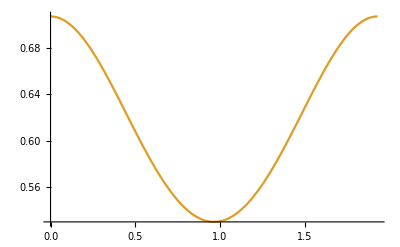

```mathematica
Plot[{Re[PhaseRow.E1+PhaseColumn.E2-PhaseRow[[1]]],κ/(A[x])^2 /. Sol},{x,0,T}]
```

```mathematica
PhaseRow
```

{0.61599213722764,0.044154492781239+6.7756328992307×10^-8 ⅈ,0.0013619844692796+1.0774547180413×10^-8 ⅈ,0.000039611878514307+1.1555069227008×10^-8 ⅈ,1.148585807981×10^-6+9.8466061589532×10^-9 ⅈ,3.4217483092075×10^-8+7.2038921486463×10^-9 ⅈ,1.3474989837864×10^-9+4.5309095829633×10^-9 ⅈ,5.0896172509353×10^-10+4.3012118855957×10^-9 ⅈ,6.8760764501026×10^-10+3.8048818523977×10^-9 ⅈ,8.1479067917077×10^-10+2.8804338866408×10^-9 ⅈ,2.4081858464126×10^-10+2.9323352094116×10^-9 ⅈ,7.6421560979644×10^-10+2.7127023734724×10^-9 ⅈ,8.8525702454965×10^-10+2.0470275934983×10^-9 ⅈ,2.8736385146982×10^-10+1.9424970757309×10^-9 ⅈ,5.3395569008772×10^-10+2.1709011989068×10^-9 ⅈ,7.3949320713472×10^-10+1.8659016477779×10^-9 ⅈ,5.959804867169×10^-10+1.5403808382552×10^-9 ⅈ,5.1672263748179×10^-10+1.703357150697×10^-9 ⅈ,6.5123864465954×10^-10+1.6095612248847×10^-9 ⅈ,6.9059430229398×10^-10+1.4078758894702×10^-9 ⅈ,6.4957421265611×10^-10+1.4430107417798×10^-9 ⅈ}

```mathematica
(* The Phase agrees pretty well with the the first NMode terms in the Fourier series. *)
```

```mathematica
Plot[Re[DerivativePhaseRow.E1+DerivativePhaseColumn.E2-DerivativePhaseRow[[1]]],{x,0,T}]
```

-Graphics-

```mathematica
(* The should be S_yy. There is some oscillation/ Gibbs phenomenon but it is not bad. *)
```

```mathematica
Syy = ToeplitzMatrix[DerivativePhaseRow,DerivativePhaseColumn];
```

```mathematica
Sy = ToeplitzMatrix[PhaseRow,PhaseColumn];
```

```mathematica
fa2 = ToeplitzMatrix[PotentialRow,PotentialColumn];
```

```mathematica
ffprime = ToeplitzMatrix[PotentialRow+2DerivativePotentialRow,PotentialColumn+2DerivativePotentialColumn];
```

```mathematica
Sy2 = ToeplitzMatrix[PhaseSquaredRow,PhaseSquaredColumn];
```

```mathematica
der1 = Table[2 Pi I k/T,{k,-NModes/2,NModes/2}];
```

```mathematica
Dimensions[der1]
```

{21}

```mathematica
Dimensions[Syy]
```

{21,21}

```mathematica
D1 = DiagonalMatrix[der1];
```

```mathematica
der2 = der1^2;
```

```mathematica
D2 = DiagonalMatrix[der2];
```

```mathematica
A11= Syy + 2 Sy . D1;
```

```mathematica
MatrixForm[A11]
```

(-40.131689739517 ⅈ | -4.193587902×10^-6-2.7328184613422 ⅈ | -6.317624569×10^-7-0.07985956534681 ⅈ | -6.3988768905×10^-7-0.0021935959797096 ⅈ | -5.132025809768×10^-7-0.000059863996956273 ⅈ | -3.5199844343092×10^-7-1.6719435185877×10^-6 ⅈ | -2.0663111205893×10^-7-6.1452387963117×10^-8 ⅈ | -1.8214467166382×10^-7-2.155315031493×10^-8 ⅈ | -1.4873209779902×10^-7-2.6878450231134×10^-8 ⅈ | -1.0321263801477×10^-7-2.9195842965568×10^-8 ⅈ | -9.5520348170353×10^-8-7.84462669104×10^-9 ⅈ | -7.9529259454537×10^-8-2.240478059998×10^-8 ⅈ | -5.3345275892798×10^-8-2.3069684239054×10^-8 ⅈ | -4.4293571034691×10^-8-6.552581894154×10^-9 ⅈ | -4.243005459215×10^-8-1.04361124733×10^-8 ⅈ | -3.039072314709×10^-8-1.204443618663×10^-8 ⅈ | -2.007106329629×10^-8-7.765587428234×10^-9 ⅈ | -1.664597562763×10^-8-5.049647060951×10^-9 ⅈ | -1.048623964334×10^-8-4.242798836928×10^-9 ⅈ | -4.58613308298×10^-9-2.2495998407×10^-9 ⅈ | 0.+0. ⅈ
4.193587902×10^-6-2.7328184613422 ⅈ | -36.118520765566 ⅈ | -3.752157596×10^-6-2.4451533601482 ⅈ | -5.615666284×10^-7-0.070986280308276 ⅈ | -5.6460678446×10^-7-0.0019355258644497 ⅈ | -4.490522583547×10^-7-0.000052380997336739 ⅈ | -3.0506531764013×10^-7-1.4490177161094×10^-6 ⅈ | -1.771123817648×10^-7-5.2673475396957×10^-8 ⅈ | -1.5412241448477×10^-7-1.823728103571×10^-8 ⅈ | -1.2394341483251×10^-7-2.239870852595×10^-8 ⅈ | -8.444670383027×10^-8-2.3887507880919×10^-8 ⅈ | -7.6416278536283×10^-8-6.275701352832×10^-9 ⅈ | -6.1856090686862×10^-8-1.742594046665×10^-8 ⅈ | -4.0008956919598×10^-8-1.730226317929×10^-8 ⅈ | -3.163826502478×10^-8-4.680415638681×10^-9 ⅈ | -2.828670306143×10^-8-6.957408315532×10^-9 ⅈ | -1.823443388825×10^-8-7.226661711977×10^-9 ⅈ | -1.003553164814×10^-8-3.882793714117×10^-9 ⅈ | -5.548658542544×10^-9-1.68321568698×10^-9 ⅈ | 0.+0. ⅈ | 4.58613308298×10^-9+2.2495998407×10^-9 ⅈ
6.317624569×10^-7-0.07985956534681 ⅈ | 3.752157596×10^-6-2.4451533601482 ⅈ | -32.105351791614 ⅈ | -3.310727291×10^-6-2.1574882589543 ⅈ | -4.913707998×10^-7-0.062112995269741 ⅈ | -4.8932587987×10^-7-0.0016774557491897 ⅈ | -3.849019357326×10^-7-0.000044897997717205 ⅈ | -2.5813219184934×10^-7-1.226091913631×10^-6 ⅈ | -1.4759365147066×10^-7-4.3894562830798×10^-8 ⅈ | -1.2610015730572×10^-7-1.492141175649×10^-8 ⅈ | -9.915473186601×10^-8-1.791896682076×10^-8 ⅈ | -6.5680769645766×10^-8-1.857917279627×10^-8 ⅈ | -5.7312208902212×10^-8-4.706776014624×10^-9 ⅈ | -4.418292191919×10^-8-1.244710033332×10^-8 ⅈ | -2.66726379464×10^-8-1.153484211953×10^-8 ⅈ | -1.898295901487×10^-8-2.808249383209×10^-9 ⅈ | -1.414335153072×10^-8-3.478704157766×10^-9 ⅈ | -6.078144629418×10^-9-2.40888723733×10^-9 ⅈ | 0.+0. ⅈ | 5.54865854254×10^-9+1.68321568698×10^-9 ⅈ | 1.048623964334×10^-8+4.242798836928×10^-9 ⅈ
6.3988768905×10^-7-0.0021935959797096 ⅈ | 5.615666284×10^-7-0.070986280308276 ⅈ | 3.310727291×10^-6-2.1574882589543 ⅈ | -28.092182817662 ⅈ | -2.86929699×10^-6-1.8698231577604 ⅈ | -4.211749713×10^-7-0.053239710231207 ⅈ | -4.1404497527×10^-7-0.0014193856339298 ⅈ | -3.20751613111×10^-7-0.00003741499809767 ⅈ | -2.1119906605855×10^-7-1.0031661111526×10^-6 ⅈ | -1.1807492117653×10^-7-3.5115650264638×10^-8 ⅈ | -9.8077900126672×10^-8-1.160554247727×10^-8 ⅈ | -7.4366048899508×10^-8-1.343922511557×10^-8 ⅈ | -4.6914835461261×10^-8-1.327083771162×10^-8 ⅈ | -3.820813926814×10^-8-3.137850676416×10^-9 ⅈ | -2.650975315151×10^-8-7.468260199995×10^-9 ⅈ | -1.33363189732×10^-8-5.767421059764×10^-9 ⅈ | -6.327653004956×10^-9-9.36083127736×10^-10 ⅈ | 0.+0. ⅈ | 6.078144629418×10^-9+2.40888723733×10^-9 ⅈ | 1.003553164814×10^-8+3.882793714117×10^-9 ⅈ | 1.664597562763×10^-8+5.049647060951×10^-9 ⅈ
5.132025809768×10^-7-0.000059863996956273 ⅈ | 5.6460678446×10^-7-0.0019355258644497 ⅈ | 4.913707998×10^-7-0.062112995269741 ⅈ | 2.86929699×10^-6-1.8698231577604 ⅈ | -24.07901384371 ⅈ | -2.42786668×10^-6-1.5821580565665 ⅈ | -3.509791427×10^-7-0.044366425192672 ⅈ | -3.3876407068×10^-7-0.0011613155186698 ⅈ | -2.56601290488×10^-7-0.000029931998478136 ⅈ | -1.6426594026776×10^-7-7.8024030867428×10^-7 ⅈ | -8.8556190882398×10^-8-2.6336737698479×10^-8 ⅈ | -7.0055642947623×10^-8-8.28967319805×10^-9 ⅈ | -4.9577365933005×10^-8-8.959483410378×10^-9 ⅈ | -2.814890127676×10^-8-7.962502626973×10^-9 ⅈ | -1.910406963407×10^-8-1.56892533821×10^-9 ⅈ | -8.836584383837×10^-9-2.48942006666×10^-9 ⅈ | 0.+0. ⅈ | 6.327653004956×10^-9+9.36083127736×10^-10 ⅈ | 1.414335153072×10^-8+3.478704157766×10^-9 ⅈ | 1.823443388825×10^-8+7.226661711977×10^-9 ⅈ | 2.007106329629×10^-8+7.765587428234×10^-9 ⅈ
3.5199844343092×10^-7-1.6719435185877×10^-6 ⅈ | 4.490522583547×10^-7-0.000052380997336739 ⅈ | 4.8932587987×10^-7-0.0016774557491897 ⅈ | 4.211749713×10^-7-0.053239710231207 ⅈ | 2.42786668×10^-6-1.5821580565665 ⅈ | -20.065844869759 ⅈ | -1.98643637×10^-6-1.2944929553726 ⅈ | -2.807833142×10^-7-0.035493140154138 ⅈ | -2.6348316608×10^-7-0.00090324540340984 ⅈ | -1.92450967866×10^-7-0.000022448998858602 ⅈ | -1.17332814477×10^-7-5.5731450619591×10^-7 ⅈ | -5.9037460588265×10^-8-1.755782513232×10^-8 ⅈ | -4.203338576857×10^-8-4.97380391883×10^-9 ⅈ | -2.47886829665×10^-8-4.479741705189×10^-9 ⅈ | -9.382967092252×10^-9-2.654167542324×10^-9 ⅈ | 0.+0. ⅈ | 8.836584383837×10^-9+2.48942006666×10^-9 ⅈ | 1.33363189732×10^-8+5.767421059764×10^-9 ⅈ | 1.898295901487×10^-8+2.808249383209×10^-9 ⅈ | 2.828670306143×10^-8+6.957408315532×10^-9 ⅈ | 3.039072314709×10^-8+1.204443618663×10^-8 ⅈ
2.0663111205893×10^-7-6.1452387963117×10^-8 ⅈ | 3.0506531764013×10^-7-1.4490177161094×10^-6 ⅈ | 3.849019357326×10^-7-0.000044897997717205 ⅈ | 4.1404497527×10^-7-0.0014193856339298 ⅈ | 3.509791427×10^-7-0.044366425192672 ⅈ | 1.98643637×10^-6-1.2944929553726 ⅈ | -16.052675895807 ⅈ | -1.54500607×10^-6-1.0068278541787 ⅈ | -2.105874856×10^-7-0.026619855115603 ⅈ | -1.8820226149×10^-7-0.00064517528814989 ⅈ | -1.28300645244×10^-7-0.000014965999239068 ⅈ | -7.039968868618×10^-8-3.3438870371755×10^-7 ⅈ | -2.951873029413×10^-8-8.77891256616×10^-9 ⅈ | -1.401112858952×10^-8-1.65793463961×10^-9 ⅈ | 0.+0. ⅈ | 9.382967092252×10^-9+2.65416754232×10^-9 ⅈ | 1.910406963407×10^-8+1.56892533821×10^-9 ⅈ | 2.650975315151×10^-8+7.468260199995×10^-9 ⅈ | 2.66726379464×10^-8+1.153484211953×10^-8 ⅈ | 3.163826502478×10^-8+4.680415638681×10^-9 ⅈ | 4.243005459215×10^-8+1.04361124733×10^-8 ⅈ
1.8214467166382×10^-7-2.155315031493×10^-8 ⅈ | 1.771123817648×10^-7-5.2673475396957×10^-8 ⅈ | 2.5813219184934×10^-7-1.226091913631×10^-6 ⅈ | 3.20751613111×10^-7-0.00003741499809767 ⅈ | 3.3876407068×10^-7-0.0011613155186698 ⅈ | 2.807833142×10^-7-0.035493140154138 ⅈ | 1.54500607×10^-6-1.0068278541787 ⅈ | -12.039506921855 ⅈ | -1.10357576×10^-6-0.71916275298478 ⅈ | -1.40391657×10^-7-0.017746570077069 ⅈ | -1.1292135689×10^-7-0.00038710517288993 ⅈ | -6.41503226221×10^-8-7.4829996195341×10^-6 ⅈ | -2.346656289539×10^-8-1.114629012392×10^-7 ⅈ | 0.+0. ⅈ | 1.401112858952×10^-8+1.65793463961×10^-9 ⅈ | 2.47886829665×10^-8+4.479741705189×10^-9 ⅈ | 2.814890127676×10^-8+7.962502626973×10^-9 ⅈ | 3.820813926814×10^-8+3.137850676416×10^-9 ⅈ | 4.418292191919×10^-8+1.244710033332×10^-8 ⅈ | 4.00089569196×10^-8+1.730226317929×10^-8 ⅈ | 4.429357103469×10^-8+6.552581894154×10^-9 ⅈ
1.4873209779902×10^-7-2.687845023113×10^-8 ⅈ | 1.5412241448477×10^-7-1.823728103571×10^-8 ⅈ | 1.4759365147066×10^-7-4.3894562830798×10^-8 ⅈ | 2.111990660586×10^-7-1.0031661111526×10^-6 ⅈ | 2.56601290488×10^-7-0.000029931998478136 ⅈ | 2.6348316608×10^-7-0.00090324540340984 ⅈ | 2.105874856×10^-7-0.026619855115603 ⅈ | 1.10357576×10^-6-0.71916275298478 ⅈ | -8.0263379479034 ⅈ | -6.62145458×10^-7-0.43149765179087 ⅈ | -7.01958285×10^-8-0.0088732850385345 ⅈ | -3.76404523×10^-8-0.00012903505763 ⅈ | 0.+0. ⅈ | 2.346656289539×10^-8+1.114629012392×10^-7 ⅈ | 2.951873029413×10^-8+8.77891256616×10^-9 ⅈ | 4.203338576857×10^-8+4.97380391883×10^-9 ⅈ | 4.957736593301×10^-8+8.959483410378×10^-9 ⅈ | 4.691483546126×10^-8+1.327083771162×10^-8 ⅈ | 5.731220890221×10^-8+4.706776014624×10^-9 ⅈ | 6.185609068686×10^-8+1.742594046665×10^-8 ⅈ | 5.33452758928×10^-8+2.306968423905×10^-8 ⅈ
1.0321263801477×10^-7-2.919584296557×10^-8 ⅈ | 1.2394341483251×10^-7-2.239870852595×10^-8 ⅈ | 1.2610015730572×10^-7-1.492141175649×10^-8 ⅈ | 1.1807492117653×10^-7-3.511565026464×10^-8 ⅈ | 1.642659402678×10^-7-7.8024030867428×10^-7 ⅈ | 1.92450967866×10^-7-0.000022448998858602 ⅈ | 1.8820226149×10^-7-0.00064517528814989 ⅈ | 1.40391657×10^-7-0.017746570077069 ⅈ | 6.62145458×10^-7-0.43149765179087 ⅈ | -4.0131689739517 ⅈ | -2.2071515×10^-7-0.14383255059696 ⅈ | 0.+0. ⅈ | 3.76404523×10^-8+0.00012903505763 ⅈ | 6.41503226221×10^-8+7.482999619534×10^-6 ⅈ | 7.039968868618×10^-8+3.343887037175×10^-7 ⅈ | 5.903746058827×10^-8+1.755782513232×10^-8 ⅈ | 7.005564294762×10^-8+8.28967319805×10^-9 ⅈ | 7.436604889951×10^-8+1.343922511557×10^-8 ⅈ | 6.568076964577×10^-8+1.857917279627×10^-8 ⅈ | 7.641627853628×10^-8+6.275701352832×10^-9 ⅈ | 7.952925945454×10^-8+2.240478059998×10^-8 ⅈ
9.5520348170353×10^-8-7.84462669104×10^-9 ⅈ | 8.444670383027×10^-8-2.388750788092×10^-8 ⅈ | 9.915473186601×10^-8-1.791896682076×10^-8 ⅈ | 9.8077900126672×10^-8-1.160554247727×10^-8 ⅈ | 8.8556190882398×10^-8-2.633673769848×10^-8 ⅈ | 1.17332814477×10^-7-5.5731450619591×10^-7 ⅈ | 1.28300645244×10^-7-0.000014965999239068 ⅈ | 1.1292135689×10^-7-0.00038710517288993 ⅈ | 7.01958285×10^-8-0.0088732850385345 ⅈ | 2.2071515×10^-7-0.14383255059696 ⅈ | 0 | 2.2071515×10^-7+0.14383255059696 ⅈ | 7.01958285×10^-8+0.0088732850385345 ⅈ | 1.1292135689×10^-7+0.00038710517288993 ⅈ | 1.28300645244×10^-7+0.000014965999239068 ⅈ | 1.17332814477×10^-7+5.5731450619591×10^-7 ⅈ | 8.8556190882398×10^-8+2.633673769848×10^-8 ⅈ | 9.8077900126672×10^-8+1.160554247727×10^-8 ⅈ | 9.915473186601×10^-8+1.791896682076×10^-8 ⅈ | 8.444670383027×10^-8+2.388750788092×10^-8 ⅈ | 9.5520348170353×10^-8+7.84462669104×10^-9 ⅈ
7.952925945454×10^-8-2.240478059998×10^-8 ⅈ | 7.641627853628×10^-8-6.275701352832×10^-9 ⅈ | 6.568076964577×10^-8-1.857917279627×10^-8 ⅈ | 7.436604889951×10^-8-1.343922511557×10^-8 ⅈ | 7.005564294762×10^-8-8.28967319805×10^-9 ⅈ | 5.903746058827×10^-8-1.755782513232×10^-8 ⅈ | 7.039968868618×10^-8-3.343887037175×10^-7 ⅈ | 6.41503226221×10^-8-7.482999619534×10^-6 ⅈ | 3.76404523×10^-8-0.00012903505763 ⅈ | 0.+0. ⅈ | -2.2071515×10^-7+0.14383255059696 ⅈ | 4.0131689739517 ⅈ | 6.62145458×10^-7+0.43149765179087 ⅈ | 1.40391657×10^-7+0.017746570077069 ⅈ | 1.8820226149×10^-7+0.00064517528814989 ⅈ | 1.92450967866×10^-7+0.000022448998858602 ⅈ | 1.642659402678×10^-7+7.8024030867428×10^-7 ⅈ | 1.1807492117653×10^-7+3.511565026464×10^-8 ⅈ | 1.2610015730572×10^-7+1.492141175649×10^-8 ⅈ | 1.2394341483251×10^-7+2.239870852595×10^-8 ⅈ | 1.0321263801477×10^-7+2.919584296557×10^-8 ⅈ
5.33452758928×10^-8-2.306968423905×10^-8 ⅈ | 6.185609068686×10^-8-1.742594046665×10^-8 ⅈ | 5.731220890221×10^-8-4.706776014624×10^-9 ⅈ | 4.691483546126×10^-8-1.327083771162×10^-8 ⅈ | 4.957736593301×10^-8-8.959483410378×10^-9 ⅈ | 4.203338576857×10^-8-4.97380391883×10^-9 ⅈ | 2.951873029413×10^-8-8.77891256616×10^-9 ⅈ | 2.346656289539×10^-8-1.114629012392×10^-7 ⅈ | 0.+0. ⅈ | -3.76404523×10^-8+0.00012903505763 ⅈ | -7.01958285×10^-8+0.0088732850385345 ⅈ | -6.62145458×10^-7+0.43149765179087 ⅈ | 8.0263379479034 ⅈ | 1.10357576×10^-6+0.71916275298478 ⅈ | 2.105874856×10^-7+0.026619855115603 ⅈ | 2.6348316608×10^-7+0.00090324540340984 ⅈ | 2.56601290488×10^-7+0.000029931998478136 ⅈ | 2.111990660586×10^-7+1.0031661111526×10^-6 ⅈ | 1.4759365147066×10^-7+4.3894562830798×10^-8 ⅈ | 1.5412241448477×10^-7+1.823728103571×10^-8 ⅈ | 1.4873209779902×10^-7+2.687845023113×10^-8 ⅈ
4.429357103469×10^-8-6.552581894154×10^-9 ⅈ | 4.00089569196×10^-8-1.730226317929×10^-8 ⅈ | 4.418292191919×10^-8-1.244710033332×10^-8 ⅈ | 3.820813926814×10^-8-3.137850676416×10^-9 ⅈ | 2.814890127676×10^-8-7.962502626973×10^-9 ⅈ | 2.47886829665×10^-8-4.479741705189×10^-9 ⅈ | 1.401112858952×10^-8-1.65793463961×10^-9 ⅈ | 0.+0. ⅈ | -2.346656289539×10^-8+1.114629012392×10^-7 ⅈ | -6.41503226221×10^-8+7.4829996195341×10^-6 ⅈ | -1.1292135689×10^-7+0.00038710517288993 ⅈ | -1.40391657×10^-7+0.017746570077069 ⅈ | -1.10357576×10^-6+0.71916275298478 ⅈ | 12.039506921855 ⅈ | 1.54500607×10^-6+1.0068278541787 ⅈ | 2.807833142×10^-7+0.035493140154138 ⅈ | 3.3876407068×10^-7+0.0011613155186698 ⅈ | 3.20751613111×10^-7+0.00003741499809767 ⅈ | 2.5813219184934×10^-7+1.226091913631×10^-6 ⅈ | 1.771123817648×10^-7+5.2673475396957×10^-8 ⅈ | 1.8214467166382×10^-7+2.155315031493×10^-8 ⅈ
4.243005459215×10^-8-1.04361124733×10^-8 ⅈ | 3.163826502478×10^-8-4.680415638681×10^-9 ⅈ | 2.66726379464×10^-8-1.153484211953×10^-8 ⅈ | 2.650975315151×10^-8-7.468260199995×10^-9 ⅈ | 1.910406963407×10^-8-1.56892533821×10^-9 ⅈ | 9.382967092252×10^-9-2.65416754232×10^-9 ⅈ | 0.+0. ⅈ | -1.401112858952×10^-8+1.65793463961×10^-9 ⅈ | -2.951873029413×10^-8+8.77891256616×10^-9 ⅈ | -7.039968868618×10^-8+3.3438870371755×10^-7 ⅈ | -1.28300645244×10^-7+0.000014965999239068 ⅈ | -1.8820226149×10^-7+0.00064517528814989 ⅈ | -2.105874856×10^-7+0.026619855115603 ⅈ | -1.54500607×10^-6+1.0068278541787 ⅈ | 16.052675895807 ⅈ | 1.98643637×10^-6+1.2944929553726 ⅈ | 3.509791427×10^-7+0.044366425192672 ⅈ | 4.1404497527×10^-7+0.0014193856339298 ⅈ | 3.849019357326×10^-7+0.000044897997717205 ⅈ | 3.0506531764013×10^-7+1.4490177161094×10^-6 ⅈ | 2.0663111205893×10^-7+6.1452387963117×10^-8 ⅈ
3.039072314709×10^-8-1.204443618663×10^-8 ⅈ | 2.828670306143×10^-8-6.957408315532×10^-9 ⅈ | 1.898295901487×10^-8-2.808249383209×10^-9 ⅈ | 1.33363189732×10^-8-5.767421059764×10^-9 ⅈ | 8.836584383837×10^-9-2.48942006666×10^-9 ⅈ | 0.+0. ⅈ | -9.382967092252×10^-9+2.654167542324×10^-9 ⅈ | -2.47886829665×10^-8+4.479741705189×10^-9 ⅈ | -4.203338576857×10^-8+4.97380391883×10^-9 ⅈ | -5.9037460588265×10^-8+1.755782513232×10^-8 ⅈ | -1.17332814477×10^-7+5.5731450619591×10^-7 ⅈ | -1.92450967866×10^-7+0.000022448998858602 ⅈ | -2.6348316608×10^-7+0.00090324540340984 ⅈ | -2.807833142×10^-7+0.035493140154138 ⅈ | -1.98643637×10^-6+1.2944929553726 ⅈ | 20.065844869759 ⅈ | 2.42786668×10^-6+1.5821580565665 ⅈ | 4.211749713×10^-7+0.053239710231207 ⅈ | 4.8932587987×10^-7+0.0016774557491897 ⅈ | 4.490522583547×10^-7+0.000052380997336739 ⅈ | 3.5199844343092×10^-7+1.6719435185877×10^-6 ⅈ
2.007106329629×10^-8-7.765587428234×10^-9 ⅈ | 1.823443388825×10^-8-7.226661711977×10^-9 ⅈ | 1.414335153072×10^-8-3.478704157766×10^-9 ⅈ | 6.327653004956×10^-9-9.36083127736×10^-10 ⅈ | 0.+0. ⅈ | -8.836584383837×10^-9+2.48942006666×10^-9 ⅈ | -1.910406963407×10^-8+1.56892533821×10^-9 ⅈ | -2.814890127676×10^-8+7.962502626973×10^-9 ⅈ | -4.9577365933005×10^-8+8.959483410378×10^-9 ⅈ | -7.0055642947623×10^-8+8.28967319805×10^-9 ⅈ | -8.8556190882398×10^-8+2.6336737698479×10^-8 ⅈ | -1.6426594026776×10^-7+7.8024030867428×10^-7 ⅈ | -2.56601290488×10^-7+0.000029931998478136 ⅈ | -3.3876407068×10^-7+0.0011613155186698 ⅈ | -3.509791427×10^-7+0.044366425192672 ⅈ | -2.42786668×10^-6+1.5821580565665 ⅈ | 24.07901384371 ⅈ | 2.86929699×10^-6+1.8698231577604 ⅈ | 4.913707998×10^-7+0.062112995269741 ⅈ | 5.6460678446×10^-7+0.0019355258644497 ⅈ | 5.132025809768×10^-7+0.000059863996956273 ⅈ
1.664597562763×10^-8-5.049647060951×10^-9 ⅈ | 1.003553164814×10^-8-3.882793714117×10^-9 ⅈ | 6.078144629418×10^-9-2.40888723733×10^-9 ⅈ | 0.+0. ⅈ | -6.327653004956×10^-9+9.36083127736×10^-10 ⅈ | -1.33363189732×10^-8+5.767421059764×10^-9 ⅈ | -2.650975315151×10^-8+7.468260199995×10^-9 ⅈ | -3.820813926814×10^-8+3.137850676416×10^-9 ⅈ | -4.6914835461261×10^-8+1.327083771162×10^-8 ⅈ | -7.4366048899508×10^-8+1.343922511557×10^-8 ⅈ | -9.8077900126672×10^-8+1.160554247727×10^-8 ⅈ | -1.1807492117653×10^-7+3.5115650264638×10^-8 ⅈ | -2.1119906605855×10^-7+1.0031661111526×10^-6 ⅈ | -3.20751613111×10^-7+0.00003741499809767 ⅈ | -4.1404497527×10^-7+0.0014193856339298 ⅈ | -4.211749713×10^-7+0.053239710231207 ⅈ | -2.86929699×10^-6+1.8698231577604 ⅈ | 28.092182817662 ⅈ | 3.310727291×10^-6+2.1574882589543 ⅈ | 5.615666284×10^-7+0.070986280308276 ⅈ | 6.3988768905×10^-7+0.0021935959797096 ⅈ
1.048623964334×10^-8-4.242798836928×10^-9 ⅈ | 5.54865854254×10^-9-1.68321568698×10^-9 ⅈ | 0.+0. ⅈ | -6.078144629418×10^-9+2.40888723733×10^-9 ⅈ | -1.414335153072×10^-8+3.478704157766×10^-9 ⅈ | -1.898295901487×10^-8+2.808249383209×10^-9 ⅈ | -2.66726379464×10^-8+1.153484211953×10^-8 ⅈ | -4.418292191919×10^-8+1.244710033332×10^-8 ⅈ | -5.7312208902212×10^-8+4.706776014624×10^-9 ⅈ | -6.5680769645766×10^-8+1.857917279627×10^-8 ⅈ | -9.915473186601×10^-8+1.791896682076×10^-8 ⅈ | -1.2610015730572×10^-7+1.492141175649×10^-8 ⅈ | -1.4759365147066×10^-7+4.3894562830798×10^-8 ⅈ | -2.5813219184934×10^-7+1.226091913631×10^-6 ⅈ | -3.849019357326×10^-7+0.000044897997717205 ⅈ | -4.8932587987×10^-7+0.0016774557491897 ⅈ | -4.913707998×10^-7+0.062112995269741 ⅈ | -3.310727291×10^-6+2.1574882589543 ⅈ | 32.105351791614 ⅈ | 3.752157596×10^-6+2.4451533601482 ⅈ | 6.317624569×10^-7+0.07985956534681 ⅈ
4.58613308298×10^-9-2.2495998407×10^-9 ⅈ | 0.+0. ⅈ | -5.548658542544×10^-9+1.68321568698×10^-9 ⅈ | -1.003553164814×10^-8+3.882793714117×10^-9 ⅈ | -1.823443388825×10^-8+7.226661711977×10^-9 ⅈ | -2.828670306143×10^-8+6.957408315532×10^-9 ⅈ | -3.163826502478×10^-8+4.680415638681×10^-9 ⅈ | -4.0008956919598×10^-8+1.730226317929×10^-8 ⅈ | -6.1856090686862×10^-8+1.742594046665×10^-8 ⅈ | -7.6416278536283×10^-8+6.275701352832×10^-9 ⅈ | -8.444670383027×10^-8+2.3887507880919×10^-8 ⅈ | -1.2394341483251×10^-7+2.239870852595×10^-8 ⅈ | -1.5412241448477×10^-7+1.823728103571×10^-8 ⅈ | -1.771123817648×10^-7+5.2673475396957×10^-8 ⅈ | -3.0506531764013×10^-7+1.4490177161094×10^-6 ⅈ | -4.490522583547×10^-7+0.000052380997336739 ⅈ | -5.6460678446×10^-7+0.0019355258644497 ⅈ | -5.615666284×10^-7+0.070986280308276 ⅈ | -3.752157596×10^-6+2.4451533601482 ⅈ | 36.118520765566 ⅈ | 4.193587902×10^-6+2.7328184613422 ⅈ
0.+0. ⅈ | -4.58613308298×10^-9+2.2495998407×10^-9 ⅈ | -1.048623964334×10^-8+4.242798836928×10^-9 ⅈ | -1.664597562763×10^-8+5.049647060951×10^-9 ⅈ | -2.007106329629×10^-8+7.765587428234×10^-9 ⅈ | -3.039072314709×10^-8+1.204443618663×10^-8 ⅈ | -4.243005459215×10^-8+1.04361124733×10^-8 ⅈ | -4.4293571034691×10^-8+6.552581894154×10^-9 ⅈ | -5.3345275892798×10^-8+2.3069684239054×10^-8 ⅈ | -7.9529259454537×10^-8+2.240478059998×10^-8 ⅈ | -9.5520348170353×10^-8+7.84462669104×10^-9 ⅈ | -1.0321263801477×10^-7+2.9195842965568×10^-8 ⅈ | -1.4873209779902×10^-7+2.6878450231134×10^-8 ⅈ | -1.8214467166382×10^-7+2.155315031493×10^-8 ⅈ | -2.0663111205893×10^-7+6.1452387963117×10^-8 ⅈ | -3.5199844343092×10^-7+1.6719435185877×10^-6 ⅈ | -5.132025809768×10^-7+0.000059863996956273 ⅈ | -6.3988768905×10^-7+0.0021935959797096 ⅈ | -6.317624569×10^-7+0.07985956534681 ⅈ | -4.193587902×10^-6+2.7328184613422 ⅈ | 40.131689739517 ⅈ)

```mathematica
(* ArrayFlatten sets up block matrices, as well have *)
```

```mathematica
LM = (ω+c^2/4)  IdentityMatrix[NModes+1] + D2 -Sy2 +  fa2;
```

```mathematica
Dimensions[LM]
```

{21,21}

```mathematica
LP =(ω+c^2/4)  IdentityMatrix[NModes+1] + D2 -Sy2 + ffprime;
```

```mathematica
LinearizedOperator = ArrayFlatten[{{A11,LM},{-LP,A11}}];
```

```mathematica
LMM[μ_] := (ω+c^2/4-μ^2)  IdentityMatrix[NModes+1] + D2 + 2 I μ D1 -Sy2 +  fa2;
```

```mathematica
LPM[μ_] := (ω+c^2/4-μ^2)  IdentityMatrix[NModes+1] + D2 + 2 I μ D1 -Sy2 + ffprime;
```

```mathematica
AM11[μ_] := Syy + 2 Sy . (D1 + I μ IdentityMatrix[NModes+1]);
```

```mathematica
LinOp[μ_] := ArrayFlatten[{{AM11[μ],LMM[μ]},{-LPM[μ],AM11[μ]}}];
```

```mathematica
Eigenvalues[LinOp[0]]
```

{-1.81899×10^-12-1096.75 ⅈ,2.04636×10^-12+1096.75 ⅈ,1.20511×10^-12+1016.43 ⅈ,7.15712×10^-13-1016.43 ⅈ,-1.88516×10^-13-891.05 ⅈ,5.58962×10^-13+891.05 ⅈ,-1.87781×10^-13+818.813 ⅈ,2.28531×10^-13-818.813 ⅈ,-5.99305×10^-14-706.643 ⅈ,-6.05461×10^-13+706.643 ⅈ,-7.11229×10^-13-642.433 ⅈ,9.72236×10^-13+642.433 ⅈ,-3.73082×10^-13+543.457 ⅈ,4.99556×10^-13-543.457 ⅈ,6.31335×10^-13+487.273 ⅈ,-4.71432×10^-13-487.273 ⅈ,-5.73944×10^-13+401.491 ⅈ,-3.49995×10^-13-401.491 ⅈ,-7.00598×10^-14+353.333 ⅈ,-2.16785×10^-13-353.333 ⅈ,-1.17776×10^-13+280.742 ⅈ,-4.05572×10^-13-280.742 ⅈ,1.30998×10^-13+240.611 ⅈ,8.97036×10^-14-240.611 ⅈ,-1.16606×10^-13+181.205 ⅈ,-6.59467×10^-14-181.205 ⅈ,-6.98565×10^-14-149.1 ⅈ,-7.35737×10^-14+149.1 ⅈ,4.88691×10^-14+102.862 ⅈ,7.75421×10^-14-102.862 ⅈ,4.35315×10^-14+78.7829 ⅈ,9.16195×10^-14-78.7829 ⅈ,-2.33017×10^-15+45.6302 ⅈ,9.02767×10^-14-45.6302 ⅈ,4.07018×10^-15-29.578 ⅈ,-1.35651×10^-14+29.578 ⅈ,1.38592×10^-14+7.96516 ⅈ,4.67863×10^-16-7.96516 ⅈ,-0.000316657+0.000243217 ⅈ,0.000316657-0.000243217 ⅈ,0.000316657+0.000243217 ⅈ,-0.000316657-0.000243217 ⅈ}

```mathematica
Eigenvalues[LinOp[2 Pi/T]]
```

{-2.27374×10^-13+1323.6 ⅈ,1.78845×10^-12-1235.26 ⅈ,-2.16294×10^-12+1096.68 ⅈ,8.55727×10^-13-1016.42 ⅈ,-5.03059×10^-13-891.12 ⅈ,-4.24471×10^-13+891.05 ⅈ,1.3695×10^-12+818.828 ⅈ,-8.97369×10^-13-818.813 ⅈ,1.09712×10^-12-706.643 ⅈ,1.87887×10^-14+706.643 ⅈ,-1.30823×10^-13+642.433 ⅈ,-9.51506×10^-13-642.433 ⅈ,-4.80656×10^-13-543.457 ⅈ,-4.13961×10^-13+543.457 ⅈ,8.02256×10^-13+487.273 ⅈ,-1.95586×10^-13-487.273 ⅈ,-8.25832×10^-14-401.491 ⅈ,7.58391×10^-14+401.491 ⅈ,-1.05304×10^-13+353.333 ⅈ,4.24756×10^-13-353.333 ⅈ,1.15324×10^-13-280.742 ⅈ,7.68023×10^-14+280.742 ⅈ,3.2018×10^-13+240.611 ⅈ,-8.31628×10^-14-240.611 ⅈ,3.51846×10^-13-181.205 ⅈ,8.87362×10^-15+181.205 ⅈ,-3.74855×10^-14-149.1 ⅈ,1.83465×10^-13+149.1 ⅈ,-2.31273×10^-14-102.862 ⅈ,4.56533×10^-14+102.862 ⅈ,6.48091×10^-15+78.7829 ⅈ,-3.14304×10^-15-78.7829 ⅈ,-4.07501×10^-15-45.6302 ⅈ,5.97643×10^-15+45.6302 ⅈ,-2.48405×10^-15+29.578 ⅈ,-5.30955×10^-15-29.578 ⅈ,1.86538×10^-15-7.96516 ⅈ,1.08289×10^-14+7.96516 ⅈ,0.000316657-0.000243217 ⅈ,-0.000316657+0.000243217 ⅈ,-0.000316657-0.000243217 ⅈ,0.000316657+0.000243217 ⅈ}

```mathematica
Chop[Eigenvalues[LinOp[0]]]
```

{0.-1096.75 ⅈ,0.+1096.75 ⅈ,0.+1016.43 ⅈ,0.-1016.43 ⅈ,0.-891.05 ⅈ,0.+891.05 ⅈ,0.+818.813 ⅈ,0.-818.813 ⅈ,0.-706.643 ⅈ,0.+706.643 ⅈ,0.-642.433 ⅈ,0.+642.433 ⅈ,0.+543.457 ⅈ,0.-543.457 ⅈ,0.+487.273 ⅈ,0.-487.273 ⅈ,0.+401.491 ⅈ,0.-401.491 ⅈ,0.+353.333 ⅈ,0.-353.333 ⅈ,0.+280.742 ⅈ,0.-280.742 ⅈ,0.+240.611 ⅈ,0.-240.611 ⅈ,0.+181.205 ⅈ,0.-181.205 ⅈ,0.-149.1 ⅈ,0.+149.1 ⅈ,0.+102.862 ⅈ,0.-102.862 ⅈ,0.+78.7829 ⅈ,0.-78.7829 ⅈ,0.+45.6302 ⅈ,0.-45.6302 ⅈ,0.-29.578 ⅈ,0.+29.578 ⅈ,0.+7.96516 ⅈ,0.-7.96516 ⅈ,-0.000316657+0.000243217 ⅈ,0.000316657-0.000243217 ⅈ,0.000316657+0.000243217 ⅈ,-0.000316657-0.000243217 ⅈ}

```mathematica
NS1 = Flatten[Table[Eigenvalues[LinOp[fe]],{fe,0,2 Pi/T,.004}]];
```

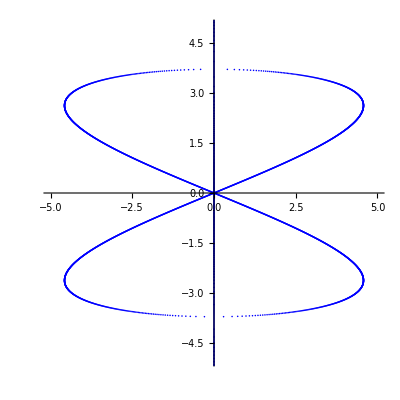

```mathematica
NumSpec=ComplexListPlot[NS1,PlotStyle->{Blue,Thickness[.04]},PlotRange->{{-5,5},{-5,5}},PlotStyle->Thick]
```

```mathematica
ModTheory=Graphics[{PointSize[Large],Red,Point[{{-3.020097895738215,+1.227452445178586 }/2,{3.020097895738215,+1.227452445178586 }/2,{0,-7.940810709488844 }/2,{0, -9.518284308442539}/2}]}];
```

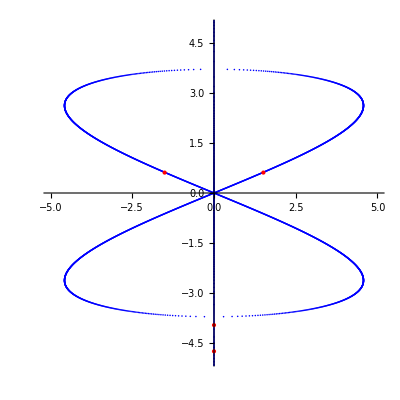

```mathematica
Show[NumSpec,ModTheory]
```

```mathematica
ζ=3; f[x_] := x^2; F[x_] := x^3/3;fp[x_] := 2x;Sol2[λ_?NumericQ] :=NDSolve[{A''[xs] - κ^2/(A[xs])^3 + (ω+c^2/4) A[xs] + ζ f[A[xs]^2] A[xs]==0,S'[xs]-κ/(A[xs])^2 ==0,λ IM1[xs]== -ω R1[xs] - R1''[xs] + 2 κ IM1'[xs]/(A[xs])^2 - 2 κ IM1[xs] A'[xs]/(A[xs])^3 + (S'[xs])^ 2 R1[xs] - ζ f[A[xs]^2] R1[xs] - 2ζ (A[xs])^2 f'[A[xs]^2] R1[xs],λ R1[xs]== ω IM1[xs] +  IM1''[xs] + 2 κ R1'[xs]/(A[xs])^2 + -2 κ R1[xs] A'[xs]/(A[xs])^3 - (S'[xs])^ 2 IM1[xs] + ζ f[A[xs]^2] IM1[xs] ,λ IM2[xs]== -ω R2[xs] - R2''[xs] + 2 κ IM2'[xs]/(A[xs])^2 - 2 κ IM2[xs] A'[xs]/(A[xs])^3 + (S'[xs])^ 2 R2[xs] - ζ f[A[xs]^2] R2[xs] - 2ζ (A[xs])^2 f'[A[xs]^2] R2[xs],λ R2[xs]== ω IM2[xs] +  IM2''[xs] + 2 κ R2'[xs]/(A[xs])^2 + -2 κ R2[xs] A'[xs]/(A[xs])^3 - (S'[xs])^ 2 IM2[xs] + ζ f[A[xs]^2] IM2[xs],λ IM3[xs]== -ω R3[xs] - R3''[xs] + 2 κ IM3'[xs]/(A[xs])^2 - 2 κ IM3[xs] A'[xs]/(A[xs])^3 + (S'[xs])^ 2 R3[xs] - ζ f[A[xs]^2] R3[xs] - 2ζ (A[xs])^2 f'[A[xs]^2] R3[xs],λ R3[xs]== ω IM3[xs] +  IM3''[xs] + 2 κ R3'[xs]/(A[xs])^2 + -2 κ R3[xs] A'[xs]/(A[xs])^3 - (S'[xs])^ 2 IM3[xs] + ζ f[A[xs]^2] IM3[xs] ,λ IM4[xs]== -ω R4[xs] - R4''[xs] + 2 κ IM4'[xs]/(A[xs])^2 - 2 κ IM4[xs] A'[xs]/(A[xs])^3 + (S'[xs])^ 2 R4[xs] - ζ f[A[xs]^2] R4[xs] - 2ζ (A[xs])^2 f'[A[xs]^2] R4[xs],λ R4[xs]== ω IM4[xs] +  IM4''[xs] + 2 κ R4'[xs]/(A[xs])^2 + -2 κ R4[xs] A'[xs]/(A[xs])^3 - (S'[xs])^ 2 IM4[xs] + ζ f[A[xs]^2] IM4[xs],λ dIM1[xs]+ IM1[xs]== -ω dR1[xs] - dR1''[xs] + 2 κ dIM1'[xs]/(A[xs])^2 - 2 κ dIM1[xs] A'[xs]/(A[xs])^3 + (S'[xs])^ 2 dR1[xs] - ζ f[A[xs]^2] dR1[xs] - 2ζ (A[xs])^2 f'[A[xs]^2] dR1[xs],λ dR1[xs]+ R1[xs]== ω dIM1[xs] +  dIM1''[xs] + 2 κ dR1'[xs]/(A[xs])^2 + -2 κ dR1[xs] A'[xs]/(A[xs])^3 - (S'[xs])^ 2 dIM1[xs] + ζ f[A[xs]^2] dIM1[xs] ,λ dIM2[xs]+ IM2[xs]== -ω dR2[xs] - dR2''[xs] + 2 κ dIM2'[xs]/(A[xs])^2 - 2 κ dIM2[xs] A'[xs]/(A[xs])^3 + (S'[xs])^ 2 dR2[xs] - ζ f[A[xs]^2] dR2[xs] - 2ζ (A[xs])^2 f'[A[xs]^2] dR2[xs],λ dR2[xs]+R2[xs]== ω dIM2[xs] +  dIM2''[xs] + 2 κ dR2'[xs]/(A[xs])^2 + -2 κ dR2[xs] A'[xs]/(A[xs])^3 - (S'[xs])^ 2 dIM2[xs] + ζ f[A[xs]^2] dIM2[xs],λ dIM3[xs]+IM3[xs]== -ω dR3[xs] - dR3''[xs] + 2 κ dIM3'[xs]/(A[xs])^2 - 2 κ dIM3[xs] A'[xs]/(A[xs])^3 + (S'[xs])^ 2 dR3[xs] - ζ f[A[xs]^2] dR3[xs] - 2ζ (A[xs])^2 f'[A[xs]^2] dR3[xs],λ dR3[xs]+R3[xs]== ω dIM3[xs] +  dIM3''[xs] + 2 κ dR3'[xs]/(A[xs])^2 + -2 κ dR3[xs] A'[xs]/(A[xs])^3 - (S'[xs])^ 2 dIM3[xs] + ζ f[A[xs]^2] dIM3[xs] ,λ dIM4[xs]+IM4[xs]== -ω dR4[xs] - dR4''[xs] + 2 κ dIM4'[xs]/(A[xs])^2 - 2 κ dIM4[xs] A'[xs]/(A[xs])^3 + (S'[xs])^ 2 dR4[xs] - ζ f[A[xs]^2] dR4[xs] - 2ζ (A[xs])^2 f'[A[xs]^2] dR4[xs],λ dR4[xs]+R4[xs]== ω dIM4[xs] +  dIM4''[xs] + 2 κ dR4'[xs]/(A[xs])^2 + -2 κ dR4[xs] A'[xs]/(A[xs])^3 - (S'[xs])^ 2 dIM4[xs] + ζ f[A[xs]^2] dIM4[xs], A[0]== tplist[[1]],A'[0]==0,S[0]==0, R1[0]==1, R1'[0]==0,IM1[0]==0,IM1'[0]==0,R2[0]==0, R2'[0]==1,IM2[0]==0,IM2'[0]==0,R3[0]==0, R3'[0]==0,IM3[0]==1,IM3'[0]==0,R4[0]==0, R4'[0]==0,IM4[0]==0,IM4'[0]==1,dR1[0]==0, dR1'[0]==0,dIM1[0]==0,dIM1'[0]==0,dR2[0]==0, dR2'[0]==0,dIM2[0]==0,dIM2'[0]==0,dR3[0]==0, dR3'[0]==0,dIM3[0]==0,dIM3'[0]==0,dR4[0]==0, dR4'[0]==0,dIM4[0]==0,dIM4'[0]==0},{A,S,R1,IM1,R2,IM2,R3,IM3,R4,IM4,dR1,dIM1,dR2,dIM2,dR3,dIM3,dR4,dIM4},{xs,0,T}]
Invar4[l_?NumericQ] := Evaluate[{(R1[T] + R2'[T] + IM3[T]+IM4'[T]), Re[-R2[T] R1'[T]+R1[T] R2'[T]-R3[T] IM1[T]-R3'[T] IM2[T]+R1[T] IM3[T]+R2'[T] IM3[T]-R4[T] IM1'[T]-R4'[T] IM2'[T]-IM4[T] IM3'[T]+R1[T] IM4'[T]+R2'[T] IM4'[T]+IM3[T] IM4'[T]],(dR1[T] + dR2'[T] + dIM3[T]+dIM4'[T]),I Im[(-Tr[{{R1[T],R2[T],R3[T],R4[T]},{R1'[T],R2'[T],R3'[T],R4'[T]},{IM1[T],IM2[T],IM3[T],IM4[T]},{IM1'[T],IM2'[T],IM3'[T],IM4'[T]}}.{{dR1[T],dR2[T],dR3[T],dR4[T]},{dR1'[T],dR2'[T],dR3'[T],dR4'[T]},{dIM1[T],dIM2[T],dIM3[T],dIM4[T]},{dIM1'[T],dIM2'[T],dIM3'[T],dIM4'[T]}}]+ Tr[{{R1[T],R2[T],R3[T],R4[T]},{R1'[T],R2'[T],R3'[T],R4'[T]},{IM1[T],IM2[T],IM3[T],IM4[T]},{IM1'[T],IM2'[T],IM3'[T],IM4'[T]}}]Tr[{{dR1[T],dR2[T],dR3[T],dR4[T]},{dR1'[T],dR2'[T],dR3'[T],dR4'[T]},{dIM1[T],dIM2[T],dIM3[T],dIM4[T]},{dIM1'[T],dIM2'[T],dIM3'[T],dIM4'[T]}}])]}/. Sol2[l]][[1]]
```

```mathematica
MatrixForm[Chop[Evaluate[{{R1[0],R1'[0],IM1[0],IM1'[0]},{R2[0],R2'[0],IM2[0],IM2'[0]},{R3[0],R3'[0],IM3[0],IM3'[0]},{R4[0],R4'[0],IM4[0],IM4'[0]}}/. Sol2[0.0]][[1]]]]
```

(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

```mathematica
f[λ_?NumericQ] := Evaluate[(R1[T] + R2'[T] + IM3[T]+IM4'[T])/. Sol2[λ]][[1]]
df[λ_?NumericQ] := Evaluate[(dR1[T] + dR2'[T] + dIM3[T]+dIM4'[T])/. Sol2[λ]][[1]]
```

```mathematica
mono[λ_?NumericQ]:= Evaluate[{{R1[T],R2[T],R3[T],R4[T]},{R1'[T],R2'[T],R3'[T],R4'[T]},{IM1[T],IM2[T],IM3[T],IM4[T]},{IM1'[T],IM2'[T],IM3'[T],IM4'[T]}}/. Sol2[λ]][[1]]
```

```mathematica
dmono[λ_?NumericQ]:= Evaluate[{{dR1[T],dR2[T],dR3[T],dR4[T]},{dR1'[T],dR2'[T],dR3'[T],dR4'[T]},{dIM1[T],dIM2[T],dIM3[T],dIM4[T]},{dIM1'[T],dIM2'[T],dIM3'[T],dIM4'[T]}}/. Sol2[λ]][[1]]
```

```mathematica
g[λ_?NumericQ]:= ((f[λ])^2 - Tr[mono[λ].mono[λ]])/2
CP[λ_?NumericQ] := CharacteristicPolynomial[mono[λ],x]
```

```mathematica
G[{{M11_?NumericQ,M12_?NumericQ,M13_?NumericQ,M14_?NumericQ},{M21_?NumericQ,M22_?NumericQ,M23_?NumericQ,M24_?NumericQ},{M31_?NumericQ,M32_?NumericQ,M33_?NumericQ,M34_?NumericQ},{M41_?NumericQ,M42_?NumericQ,M43_?NumericQ,M44_?NumericQ}}] :=-M12 M21+M11 M22-M13 M31-M23 M32+M11 M33+M22 M33-M14 M41-M24 M42-M34 M43+M11 M44+M22 M44+M33 M44
```

```mathematica
g2[λ_?NumericQ] := G[mono[λ]]
```

```mathematica
Discriminant[x^4 - f1 x^3 + g1 x^2 - Conjugate[f1] x + 1,x ]
```

256-27 f1^4+144 f1^2 g1-128 g1^2-4 f1^2 g1^3+16 g1^4-192 f1 Conjugate[f1]+18 f1^3 g1 Conjugate[f1]-80 f1 g1^2 Conjugate[f1]-6 f1^2 Conjugate[f1]^2+144 g1 Conjugate[f1]^2+f1^2 g1^2 Conjugate[f1]^2-4 g1^3 Conjugate[f1]^2-4 f1^3 Conjugate[f1]^3+18 f1 g1 Conjugate[f1]^3-27 Conjugate[f1]^4

```mathematica
Discer[f1_?NumericQ,g1_?NumericQ] := 256-27 f1^4+144 f1^2 g1-128 g1^2-4 f1^2 g1^3+16 g1^4-192 f1 Conjugate[f1]+18 f1^3 g1 Conjugate[f1]-80 f1 g1^2 Conjugate[f1]-6 f1^2 Conjugate[f1]^2+144 g1 Conjugate[f1]^2+f1^2 g1^2 Conjugate[f1]^2-4 g1^3 Conjugate[f1]^2-4 f1^3 Conjugate[f1]^3+18 f1 g1 Conjugate[f1]^3-27 Conjugate[f1]^4
```

```mathematica
Disco[λ_?NumericQ]:= Discer[f[λ],g2[λ]]
```

```mathematica
CP = x^4 - f1[λ] x^3 + g1[λ] x^2 - f1c[λ] x + 1
```

1+x^4-x^3 f1[λ]-x f1c[λ]+x^2 g1[λ]

```mathematica
Resultant[CP,D[CP,λ],x]
```

f1'[λ]^4+f1c[λ]^2 f1'[λ]^3 f1c'[λ]-2 g1[λ] f1'[λ]^3 f1c'[λ]+2 f1'[λ]^2 f1c'[λ]^2-2 f1[λ] f1c[λ] f1'[λ]^2 f1c'[λ]^2+g1[λ]^2 f1'[λ]^2 f1c'[λ]^2+f1[λ]^2 f1'[λ] f1c'[λ]^3-2 g1[λ] f1'[λ] f1c'[λ]^3+f1c'[λ]^4-f1c[λ] f1'[λ]^3 g1'[λ]+3 f1[λ] f1'[λ]^2 f1c'[λ] g1'[λ]-f1c[λ] g1[λ] f1'[λ]^2 f1c'[λ] g1'[λ]+3 f1c[λ] f1'[λ] f1c'[λ]^2 g1'[λ]-f1[λ] g1[λ] f1'[λ] f1c'[λ]^2 g1'[λ]-f1[λ] f1c'[λ]^3 g1'[λ]+g1[λ] f1'[λ]^2 g1'[λ]^2-4 f1'[λ] f1c'[λ] g1'[λ]^2+f1[λ] f1c[λ] f1'[λ] f1c'[λ] g1'[λ]^2+g1[λ] f1c'[λ]^2 g1'[λ]^2-f1[λ] f1'[λ] g1'[λ]^3-f1c[λ] f1c'[λ] g1'[λ]^3+g1'[λ]^4

```mathematica
% /. {f1[λ]->a + I b,g1[λ]->K, f1c[λ]->a - I b,f1'[λ]->c+I d,g1'[λ]->I f,f1c'[λ]->c - I d}
```

4 d^4-(a-ⅈ b)^2 d^4-2 (a-ⅈ b) (a+ⅈ b) d^4-(a+ⅈ b)^2 d^4+2 (a-ⅈ b) d^3 f-2 (a+ⅈ b) d^3 f+4 d^2 f^2-(a-ⅈ b) (a+ⅈ b) d^2 f^2+(a-ⅈ b) d f^3-(a+ⅈ b) d f^3+f^4+4 d^4 K+(a-ⅈ b) d^3 f K-(a+ⅈ b) d^3 f K+2 d^2 f^2 K+d^4 K^2

```mathematica
Expand[%]
```

4 d^4-4 a^2 d^4-4 ⅈ b d^3 f+4 d^2 f^2-a^2 d^2 f^2-b^2 d^2 f^2-2 ⅈ b d f^3+f^4+4 d^4 K-2 ⅈ b d^3 f K+2 d^2 f^2 K+d^4 K^2

```mathematica
CP
```

1+x^4-x^3 f1[λ]-x f1c[λ]+x^2 g1[λ]

```mathematica
Resultant[CP,D[CP,λ],x] /. {f1[λ]->f1,g1[λ]->g1, f1c[λ]->Conjugate[f1],f1'[λ]->df1,g1'[λ]->dg1,f1c'[λ]->Conjugate[-df1]}
```

df1^4+dg1^4-df1 dg1^3 f1+df1^2 dg1^2 g1+4 df1 dg1^2 Conjugate[df1]-3 df1^2 dg1 f1 Conjugate[df1]+2 df1^3 g1 Conjugate[df1]+2 df1^2 Conjugate[df1]^2+dg1^2 g1 Conjugate[df1]^2-df1 dg1 f1 g1 Conjugate[df1]^2+df1^2 g1^2 Conjugate[df1]^2+dg1 f1 Conjugate[df1]^3-df1 f1^2 Conjugate[df1]^3+2 df1 g1 Conjugate[df1]^3+Conjugate[df1]^4-df1^3 dg1 Conjugate[f1]+dg1^3 Conjugate[df1] Conjugate[f1]-df1 dg1^2 f1 Conjugate[df1] Conjugate[f1]+df1^2 dg1 g1 Conjugate[df1] Conjugate[f1]+3 df1 dg1 Conjugate[df1]^2 Conjugate[f1]-2 df1^2 f1 Conjugate[df1]^2 Conjugate[f1]-df1^3 Conjugate[df1] Conjugate[f1]^2

```mathematica
Reso[{f1_?NumericQ,g1_?NumericQ,df1_?NumericQ,dg1_?NumericQ}] := Re[df1^4+dg1^4-df1 dg1^3 f1+df1^2 dg1^2 g1+4 df1 dg1^2 Conjugate[df1]-3 df1^2 dg1 f1 Conjugate[df1]+2 df1^3 g1 Conjugate[df1]+2 df1^2 Conjugate[df1]^2+dg1^2 g1 Conjugate[df1]^2-df1 dg1 f1 g1 Conjugate[df1]^2+df1^2 g1^2 Conjugate[df1]^2+dg1 f1 Conjugate[df1]^3-df1 f1^2 Conjugate[df1]^3+2 df1 g1 Conjugate[df1]^3+Conjugate[df1]^4-df1^3 dg1 Conjugate[f1]+dg1^3 Conjugate[df1] Conjugate[f1]-df1 dg1^2 f1 Conjugate[df1] Conjugate[f1]+df1^2 dg1 g1 Conjugate[df1] Conjugate[f1]+3 df1 dg1 Conjugate[df1]^2 Conjugate[f1]-2 df1^2 f1 Conjugate[df1]^2 Conjugate[f1]-df1^3 Conjugate[df1] Conjugate[f1]^2]
```

```mathematica
Reso2[l_] := Reso[Invar4[l]]
```

```mathematica
Reso2[3.8I]
```

22.4449

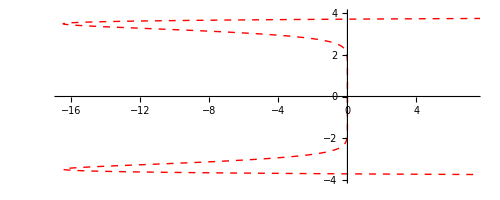

```mathematica
BifPlot=ParametricPlot[{Reso2[ll I],ll},{ll,-4,4},PlotStyle->{Thick,Red,Dashed}]
```

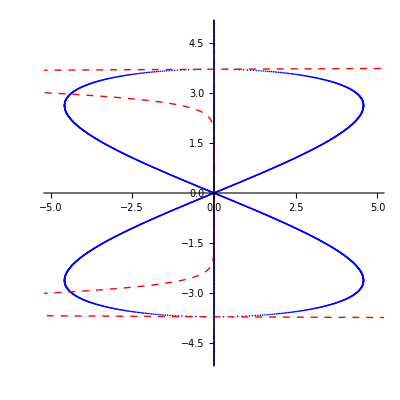

```mathematica
PaperPlot = Show[NumSpec,BifPlot]
```